```mathematica
J1 = 172; J2 = J1 + Ceiling[365/2]; (*the first one is for the 21 of June and the second one is  21st of November which are respectively summer and winter solstice in the northern hemisphere*)
 ϕ = 30; (*latitude*)
```

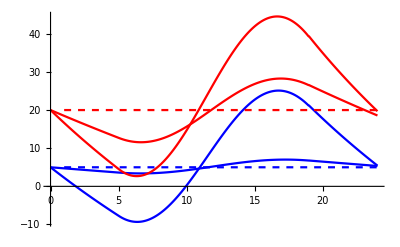

```mathematica
r1 = 6 ; r2 = 0.00825;T0 = 5; cT0=ConstantArray[T0,24];
dt = {DailyTemperature[J1,ϕ,r1,r2,T0],DailyTemperature[J1,ϕ,r1/10,r2/10,T0],DailyTemperature[J1,ϕ,r1+1.4,r2,T0+15],DailyTemperature[J1,ϕ,r1/2,r2/2.25,T0+15],cT0, cT0+15};
ListPlot[dt,Joined->True,PlotStyle-> {Blue,Blue,Red,Red,{Dashed,Blue},{Dashed,Red}}]
```

```mathematica
ff = Interpolation[DailyTemperature[J1,ϕ,r1/2,r2/2.25,T0+15]];
dT = Table[{tt,ff[tt]},{tt,0,24,1./60}];
```

```mathematica
z1 = 0.1;z2 =5; (*two body sizes: small blue, large red*)
rr1 = r1/2; rr2 = r2/2.25; (*how much solar energy is absorbed, how much is lost through emissivity and other stuff*)
rr3 =1; rK1 =1; (* a coefficient for absorption of solar radiation by the individual (the default value is maximum solar radiation), a coefficient for conductance from surface to core (the default value is that of sleeping bag *)
```

```mathematica
(*different starting time for warm-up*)
th = 2;asz= 16; prangey ={10,50}; 
t0 =6; t1 = t0 + 2; 
d1 =ThoraxT[z1,J1,ϕ,t0,t1,False,rr3,rK1,rr1,rr2,T0+15];
d2 =ThoraxT[z2,J1,ϕ,t0,t1,False,rr3,rK1,rr1,rr2,T0+15];

fig2a =ListPlot[{d1[[All,{1,3}]],d1[[All,{1,2}]],d2[[All,{1,3}]],d2[[All,{1,2}]],dT},Joined->True,PlotStyle->{{Blue,AbsoluteThickness[th]},{Blue,Dashed},{Red,AbsoluteThickness[th]},{Red,Dashed},{Black}},PlotRange->{{t0,t1},prangey},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];

(*different starting time for warm-up*)
t0 =9; t1 = t0 + 2; 
d1 =ThoraxT[z1,J1,ϕ,t0,t1,False,rr3,rK1,rr1,rr2,T0+15];
d2 =ThoraxT[z2,J1,ϕ,t0,t1,False,rr3,rK1,rr1,rr2,T0+15];

fig2b =ListPlot[{d1[[All,{1,3}]],d1[[All,{1,2}]],d2[[All,{1,3}]],d2[[All,{1,2}]],dT},Joined->True,PlotStyle->{{Blue,AbsoluteThickness[th]},{Blue,Dashed},{Red,AbsoluteThickness[th]},{Red,Dashed},{Black}},PlotRange->{{t0,t1},prangey},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];


(*different starting time for warm-up*)
t0 =12; t1 = t0 + 2;
d1 =ThoraxT[z1,J1,ϕ,t0,t1,False,rr3,rK1,rr1,rr2,T0+15];
d2 =ThoraxT[z2,J1,ϕ,t0,t1,False,rr3,rK1,rr1,rr2,T0+15];


fig2c =ListPlot[{d1[[All,{1,3}]],d1[[All,{1,2}]],d2[[All,{1,3}]],d2[[All,{1,2}]],dT},Joined->True,PlotStyle->{{Blue,AbsoluteThickness[th]},{Blue,Dashed},{Red,AbsoluteThickness[th]},{Red,Dashed},{Black}},PlotRange->{{t0,t1},prangey},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];

(*different starting time for warm-up*)
t0 =15; t1 = t0 + 2;
d1 =ThoraxT[z1,J1,ϕ,t0,t1,False,rr3,rK1,rr1,rr2,T0+15];
d2 =ThoraxT[z2,J1,ϕ,t0,t1,False,rr3,rK1,rr1,rr2,T0+15];

fig2d =ListPlot[{d1[[All,{1,3}]],d1[[All,{1,2}]],d2[[All,{1,3}]],d2[[All,{1,2}]],dT},Joined->True,PlotStyle->{{Blue,AbsoluteThickness[th]},{Blue,Dashed},{Red,AbsoluteThickness[th]},{Red,Dashed},{Black}},PlotRange->{{t0,t1},prangey},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
```

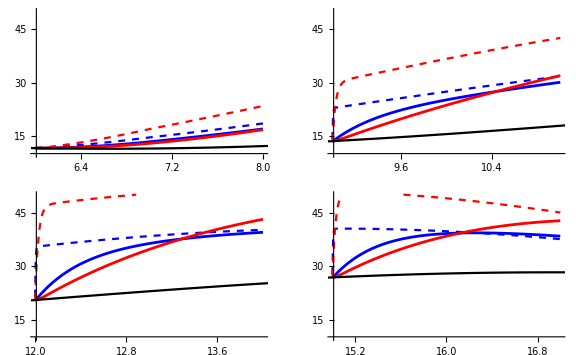

```mathematica
out = GraphicsGrid[{{fig2a,fig2b},{fig2c,fig2d}},ImageSize-> Large]
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\1 Size and range\\12 Appendix warm-up\\fig_analysis\\ecto\\r1_"<>ToString@rr1<>"_r2_"<>ToString@rr2<>"_r3_"<>ToString@rr3<>"_rK1_"<>ToString@rK1<>".png",out, ImageResolution->200]
```

C:\Users\tramiada\Documents\Projects\1 Size and range\12 Appendix warm-up\fig_analysis\ecto\r1_3_r2_0.00366667_r3_1_rK1_1.png

```mathematica
Do[
z1 = 0.1;z2 =5; (*two body sizes: small blue, large red*)
rr1 = r1/2; rr2 = r2/2.25; (*how much solar energy is absorbed, how much is lost through emissivity and other stuff*)
(*rr3 =0.; rK1 =1;*) (* a coefficient for absorption of solar radiation by the individual (the default value is maximum solar radiation), a coefficient for conductance from surface to core (the default value is that of sleeping bag *)

(*different starting time for warm-up*)
th = 2;asz= 16; prangey ={10,50}; 
t0 =6; t1 = t0 + 2; 
d1 =ThoraxT[z1,J1,ϕ,t0,t1,True,rr3,rK1,rr1,rr2,T0+15];
d2 =ThoraxT[z2,J1,ϕ,t0,t1,True,rr3,rK1,rr1,rr2,T0+15];

fig2a =ListPlot[{d1[[All,{1,3}]],d1[[All,{1,2}]],d2[[All,{1,3}]],d2[[All,{1,2}]],dT},Joined->True,PlotStyle->{{Blue,AbsoluteThickness[th]},{Blue,Dashed},{Red,AbsoluteThickness[th]},{Red,Dashed},{Black}},PlotRange->{{t0,t1},prangey},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];

(*different starting time for warm-up*)
t0 =9; t1 = t0 + 2; 
d1 =ThoraxT[z1,J1,ϕ,t0,t1,True,rr3,rK1,rr1,rr2,T0+15];
d2 =ThoraxT[z2,J1,ϕ,t0,t1,True,rr3,rK1,rr1,rr2,T0+15];

fig2b =ListPlot[{d1[[All,{1,3}]],d1[[All,{1,2}]],d2[[All,{1,3}]],d2[[All,{1,2}]],dT},Joined->True,PlotStyle->{{Blue,AbsoluteThickness[th]},{Blue,Dashed},{Red,AbsoluteThickness[th]},{Red,Dashed},{Black}},PlotRange->{{t0,t1},prangey},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];


(*different starting time for warm-up*)
t0 =12; t1 = t0 + 2;
d1 =ThoraxT[z1,J1,ϕ,t0,t1,True,rr3,rK1,rr1,rr2,T0+15];
d2 =ThoraxT[z2,J1,ϕ,t0,t1,True,rr3,rK1,rr1,rr2,T0+15];


fig2c =ListPlot[{d1[[All,{1,3}]],d1[[All,{1,2}]],d2[[All,{1,3}]],d2[[All,{1,2}]],dT},Joined->True,PlotStyle->{{Blue,AbsoluteThickness[th]},{Blue,Dashed},{Red,AbsoluteThickness[th]},{Red,Dashed},{Black}},PlotRange->{{t0,t1},prangey},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];

(*different starting time for warm-up*)
t0 =15; t1 = t0 + 2;
d1 =ThoraxT[z1,J1,ϕ,t0,t1,True,rr3,rK1,rr1,rr2,T0+15];
d2 =ThoraxT[z2,J1,ϕ,t0,t1,True,rr3,rK1,rr1,rr2,T0+15];

fig2d =ListPlot[{d1[[All,{1,3}]],d1[[All,{1,2}]],d2[[All,{1,3}]],d2[[All,{1,2}]],dT},Joined->True,PlotStyle->{{Blue,AbsoluteThickness[th]},{Blue,Dashed},{Red,AbsoluteThickness[th]},{Red,Dashed},{Black}},PlotRange->{{t0,t1},prangey},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];


out = GraphicsGrid[{{fig2a,fig2b},{fig2c,fig2d}},ImageSize-> Large];

Export["C:\\Users\\tramiada\\Documents\\Projects\\1 Size and range\\12 Appendix warm-up\\fig_analysis\\endo\\aw_0.25_r1_"<>ToString@rr1<>"_r2_"<>ToString@rr2<>"_r3_"<>ToString@rr3<>"_rK1_"<>ToString@rK1<>".png",out, ImageResolution->200];

,{rK1,{0.1,1,10}},{rr3,{0,0.5,1,2}}];
```